x'[t]-radioEsfera (Cos[ψsph[t]] θsph'[t]+Cos[θsph[t]] Sin[ψsph[t]] ϕsph'[t])

y'[t]+radioEsfera (-Sin[ψsph[t]] θsph'[t]+Cos[θsph[t]] Cos[ψsph[t]] ϕsph'[t])

{{x→InterpolatingFunction[{{0., 10.}}, <>],y→InterpolatingFunction[{{0., 10.}}, <>],ψsph→InterpolatingFunction[{{0., 10.}}, <>],θsph→InterpolatingFunction[{{0., 10.}}, <>],ϕsph→InterpolatingFunction[{{0., 10.}}, <>],αpend→InterpolatingFunction[{{0., 10.}}, <>],βpend→InterpolatingFunction[{{0., 10.}}, <>],φ1→InterpolatingFunction[{{0., 10.}}, <>],φ2→InterpolatingFunction[{{0., 10.}}, <>],γ1→InterpolatingFunction[{{0., 10.}}, <>],γ2→InterpolatingFunction[{{0., 10.}}, <>],λ1→InterpolatingFunction[{{0., 10.}}, <>],λ2→InterpolatingFunction[{{0., 10.}}, <>],VoltAlfa→InterpolatingFunction[{{0., 10.}}, <>],VoltBeta→InterpolatingFunction[{{0., 10.}}, <>],TorqueVol1CMG→InterpolatingFunction[{{0., 10.}}, <>],TorqueVol2CMG→InterpolatingFunction[{{0., 10.}}, <>],TorqueVol1Fast→InterpolatingFunction[{{0., 10.}}, <>],TorqueVol2Fast→InterpolatingFunction[{{0., 10.}}, <>]}}

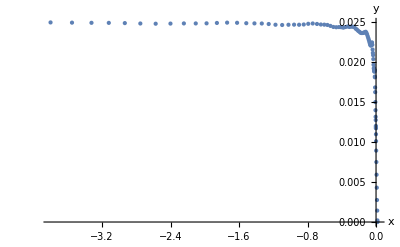

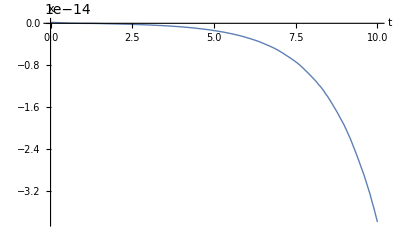

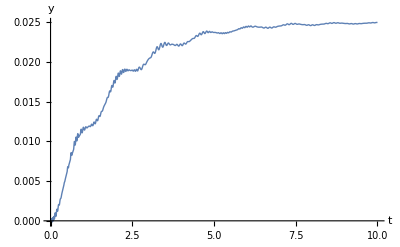

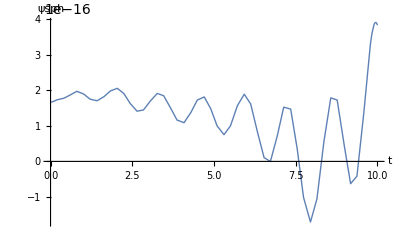

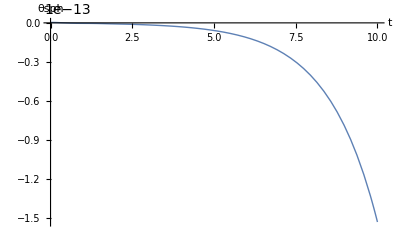

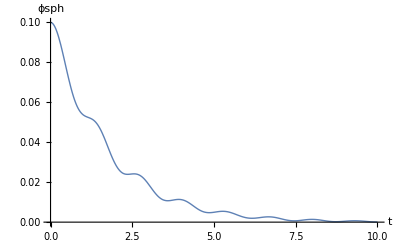

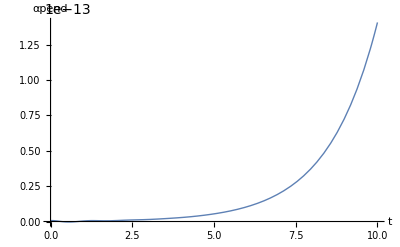

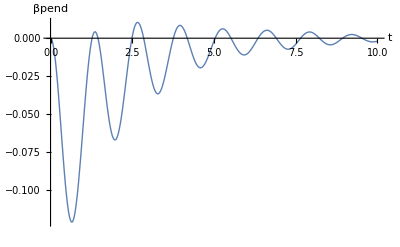

```mathematica
(*Consideramos que en el sistema tenemos solamente cuatro cuerpos, la esfera, el pendulo, y dos volantes de inercia, quiza con posibles distancias entre los centros de giro y los centro de masa de cada cuerpo, y con un sistema de referencia acoplado al centro de masa de cada cuerpo, el metodo de modelado lagrangiano intenta obtenr primero las energias cineticas y potenciales de todos los cuerpos, y usar sus expresiones simbolicas para derivar las ecuaciones diferenciales del sistema, en el caso de la energia cinetica, en cuerpos rigidos podemos distinguir dos tipos de energias mecanicas, la rotacional y la traslacional*)
ClearAll["Global`*"]
(*Representaremos TODAS las rotaciones en el sistema a traves de matrices de rotacion con argumento simbolicos. Si bien esto es molesto, nos da varias ventajas, transformar entre coordenadas entre sistemas es trivial, y la obtencion del vector de velocidad angular es una operacion sistematica. Como desventaja, existen ambiguedades bien conocidas en el uso de matrices de rotacion, en particular, la "direccion" en que las matrices transforman, y el "orden" en que las matrices se multiplican para componer una rotacion general consistente de multiples rotaciones parciales

Estas matrices de transformacion son las estandares usadas en matematicas, para expresar rotaciones de vectores COLUMNA, en Mathematica, especificamos funciones que quiza puedan tomar argumentos con la sintaxis de un guion bajo luego del argumento, y el operador dos punto igual, o de evaluacion demorada*)
Rx[θ_]:=({{1, 0, 0}, {0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}});
Ry[θ_]:=({{Cos[θ], 0, Sin[θ]}, {0, 1, 0}, {-Sin[θ], 0, Cos[θ]}});
Rz[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
(*La funcion siguiente calcula el tensor de velocidad angular (GetWx) y de este podemos obtener el vector de velocidad angular devolviendo algunos de sus componentes en ubicaciones especificas con la funcion GetW, dada cierta matriz de rotacion simbolica que describa las rotaciones que lleven de un sistema inercial O a un sistema final P, y, dependiendo de la matriz de rotacion usada, quiza obteniendo la velocidad angular de P en terminos de O, o viceversa, diremos que ω es el prefijo de las velocidades expresadas en terminos de O, en tanto Ω es el prefijo de las velocidades expresadas en terminos de P en lo sucesivo, donde O es el sistema inercial, y P el sistema acoplado al cuerpo

Las velocidades angulares son importantes, porque se necesitan para determinar las energias rotacionales de los cuerpos*)
GetWx[Rmt_] := D[Rmt, t].Transpose[Rmt];
GetW[Rmt_] := {{GetWx[Rmt][[3]][[2]]}, {GetWx[Rmt][[1]][[3]]}, {GetWx[Rmt][[2]][[1]]}};
(*Rotaciones de la esfera*)
EsfPrimRot = Rz[ψsph[t]];
EsfSecRot = Ry[θsph[t]];
EsfTerRot = Rx[ϕsph[t]];
(*Rotaciones del pendulo*)
PendSecRot = Ry[αpend[t]];
(PendPrimRot = Rx[βpend[t]];)
(*Primera rotacion al primer CMG de inercia desde el sistema del pendulo*)
Vol1Rot1 = Ry[φ1[t]];
(*Primera rotacion al segundo CMG de inercia desde el sistema del pendulo*)
Vol2Rot1 = Ry[φ2[t]];
(*Segunda rotacion del primer volante de inercia desde el sistema del CMG*)
Vol1Rot2 = Rz[γ1[t]];
(*Segunda rotacion del segundo volante de inercia desde el sistema del CMG*)
Vol2Rot2 = Rz[γ2[t]];
(*Las rotaciones se composicionan en el orden inverso al cual se declara que suceden. Esto tiene sentido, porque podemos pensar que el orden de rotaciones, digamos, para el pendulo, podria haber sido

RPend=PenSecRot.PendPrimRot.EsfTerRot.EsfSecRot.EsfPrimRot

Peo hacer esto estaria mal, porque estariamos expresando siempre rotaciones en torno a los ejes del sistema inercial O, cuando lo que queremos es expresar composciones de rotaciones, cada una de ellas rotando algun vector de posicion, con respecto al sistema acoplado al ultimo cuerpo, y asi sucesivamente. Por un artilugio matematico, es posible demostrar que la forma de expresar esta rotacion se consigue invirtiendo el orden en que las rotaciones parciales se aplican*)
REsf = EsfPrimRot.EsfSecRot.EsfTerRot;
RPend = REsf.PendPrimRot.PendSecRot;
RVol1 = RPend.Vol1Rot1.Vol1Rot2;
RVol2 = RPend.Vol2Rot1.Vol2Rot2;
(*Delta de posicion del centro de giro de la esfera al centro de masa del pendulo*)
DVecPend = RPend.{{0}, {0}, {-radioPendulo}};
(*Delta de posicion del centro de giro de la esfera al centro de masa de la esfera*)
DVecEsf = REsf.{{0}, {0}, {offsetEsf}};
(*Delta de posicion del centro de giro de la esfera al centro de masa del volante 1*)
DVecVol1=RPend.{{0},{-radioVolante},{-offsetVol}};
(*Delta de posicion del centro de giro de la esfera al centro de masa del volante 2*)
DVecVol2=RPend.{{0},{radioVolante},{-offsetVol}};
(*Velocidad angular de O en terminos del sistema de la esfera, y del sistema de la esfera en O*)
ΩEsf = -GetW[Transpose[REsf]] // Simplify;
ωEsf = GetW[REsf] // Simplify;
(*Lo mismo para el péndulo*) 
ΩPend = -GetW[Transpose[RPend]] // Simplify;
ωPend = GetW[RPend] // Simplify;
(*Volante 1*)
ΩVol1=-GetW[Transpose[RVol1]]//Simplify;
ωVol1=GetW[RVol1]//Simplify;
(*Volante 2*)
ΩVol2=-GetW[Transpose[RVol2]]//Simplify;
ωVol2=GetW[RVol2]//Simplify;
(*Tensores de inercia de los cuerpos del sistema, se asume que existen solamente tres clases de cuerpos, la esfera, el pendulo motriz, y cada volante de inercia. Esta suposicion en razonable porque estas clases de cuerpos engloban TODOS los grados de libertad rotacionales del sistema. Estos tensores de usan para obtener las energia cineticas rotacionales (que toman por parametro las inercias angulares).

Los tensores de inercia deben ser todos expresados con respecto al CENTRO DE MASA de cada cuerpo, la posible aplicacion del teorema de los ejes paralelos, donde tenga sentido, se incluye implicitamente en las expresiones de energia traslacional (que toman por parametro la masa) de los cuerpos en rotacion. Como los cuerpos se asumen simetricos al menos sobre dos planos, los tensores son todos diagonales

Para evitar transformar los tensores de inercia a otros sistemas de referencia, la velocidad que se usa en el calculo de la energia rotacional es la de O en terminos del sistema acoplado al cuerpo analizado*)
InertiaPendulo =({{IxxP, 0, 0}, {0, IyyP, 0}, {0, 0, IzzP}});
InertiaSph=({{IxxS, 0, 0}, {0, IyyS, 0}, {0, 0, IzzS}});
InertiaVolante=({{IxxV, 0, 0}, {0, IyyV, 0}, {0, 0, IzzV}});
(*Energia rotacional de la esfera*)
EROTESF = 0.5*(Transpose[ΩEsf].InertiaSph.ΩEsf)[[1]][[1]];
(*Energia rotacional del pendulo*)
EROTPEND = 0.5*(Transpose[ΩPend].InertiaPendulo.ΩPend)[[1]][[1]];
(*Energias rotacionales de los volantes*)
EROTVOL1=0.5*(Transpose[ΩVol1].InertiaVolante.ΩVol1)[[1]][[1]];
EROTVOL2=0.5*(Transpose[ΩVol2].InertiaVolante.ΩVol2)[[1]][[1]];
(*Posicion del centro GEOMETRICO de la esfera, y luego de su centro de masa*)
VecEsfera = {{x[t]}, {y[t]}, {radioEsfera}};
VecEsferaMasa = VecEsfera + DVecEsf;
(*Energia cinetica de la esfera, la posicion usada es la del centro de masa*)
VelEsfera = D[VecEsferaMasa, t];
ETRASESF = (0.5*mEsf*Transpose[VelEsfera].VelEsfera)[[1]][[1]];
(*Energia cinetica del pendulo, igualmente, debe expresarse en termino del centro de masa de la esfera, pero en este caso, se parte desde el CENTRO GEOMETRICO de la esfera para llegar al centro de masa del pendulo*)
VecPend = VecEsfera + DVecPend;
VelPend = D[VecPend, t];
ETRASPEND = (0.5*mPend*Transpose[VelPend].VelPend)[[1]][[1]];
(*Energias cineticas de los volantes*)
VecVol1=VecEsfera+DVecVol1;
VecVol2=VecEsfera+DVecVol2;
VelVol1=D[VecVol1,t];
VelVol2=D[VecVol2,t];
ETRASVOL1=(0.5*mVol*Transpose[VelVol1].VelVol1)[[1]][[1]];
ETRASVOL2=(0.5*mVol*Transpose[VelVol2].VelVol2)[[1]][[1]];
(*Energias potenciales*)
gVector = Transpose[{{0}, {0}, {g}}];
EPOTESF   = (mEsf*gVector.VecEsferaMasa)[[1]][[1]];
EPOTPEND = (mPend*gVector.VecPend)[[1]][[1]];
EPOTVOL1=(mVol*gVector.VecVol1)[[1]][[1]];
EPOTVOL2=(mVol*gVector.VecVol2)[[1]][[1]];
(*Lagrangiano*)
T=EROTESF+EROTPEND+ETRASESF+ETRASPEND+EROTVOL1+EROTVOL2+ETRASVOL1+ETRASVOL2;
V=EPOTESF+EPOTPEND+EPOTVOL1+EPOTVOL2;
Lag=T-V//Chop;
(*Aplicacion de las ecuaciones de Euler Lagrange, parte izquierda*)
EULA1 = D[D[Lag, x'[t]], t] - D[Lag, x[t]] // Chop;
EULA2 = D[D[Lag, y'[t]], t] - D[Lag, y[t]] // Chop;
EULA3 = D[D[Lag, ψsph'[t]], t] - D[Lag, ψsph[t]] // Chop;
EULA4 = D[D[Lag, θsph'[t]], t] - D[Lag, θsph[t]] // Chop;
EULA5 = D[D[Lag, ϕsph'[t]], t] - D[Lag, ϕsph[t]] // Chop;
EULA6 = D[D[Lag, αpend'[t]], t] - D[Lag, αpend[t]] // Chop;
EULA7 = D[D[Lag, βpend'[t]], t] - D[Lag, βpend[t]] // Chop;
EULA8=D[D[Lag,φ1'[t]],t]-D[Lag,φ1[t]]//Chop;
EULA9=D[D[Lag,φ2'[t]],t]-D[Lag,φ2[t]]//Chop;
EULA10=D[D[Lag,γ1'[t]],t]-D[Lag,γ1[t]]//Chop;
EULA11=D[D[Lag,γ2'[t]],t]-D[Lag,γ2[t]]//Chop;
(*Restricciones, estas especifican una condicion de no deslizamiento, de manera que podamos decir que entre la esfera y el suelo el contacto siempre garantiza que el movimiento de la esfera en sus coordenadas lineales y el que se obtien emultiplicando su radio por su velocidad angular sean siempre iguales*)
Restriccion1 = (x'[t] - radioEsfera*(ωEsf[[2]][[1]]))
Restriccion2 = (y'[t] + radioEsfera*(ωEsf[[1]][[1]]))
(*Coreficientes de los multiplicadores de lagragne, de los cuales habra tantos como se tengan restricciones, sobre cada uno de los grados de libertad del sistema, y especifican la proyeccion de la fuerza que representa el multiplcador de lagrange sobre esa coordenada generalizada, otra forma que tambien puede funcionar, paro no es tractable para el modelo completo con el voltaje de los motores, habria sido especificar fricciones viscosas con un coeficiente extremadamente alto, y asumir que el multiplicador de lagrange es en cada caso igual a la fuerza de friccion viscosa, que es el producto del coeficiente de friccion por la restriccion, que no se asume ya necesariamente cero en todo momento, un coeficiente de friccion que tienda a infinito brindaria el mismo comportamiento que el obtenible con los multplicadores*)
a11 = D[Restriccion1, x'[t]];
a12 = D[Restriccion1, y'[t]];
a13 = D[Restriccion1, ψsph'[t]];
a14 = D[Restriccion1, θsph'[t]];
a15 = D[Restriccion1, ϕsph'[t]];
a16 = D[Restriccion1, αpend'[t]];
a17 = D[Restriccion1, βpend'[t]];
a18=D[Restriccion1,φ1'[t]];
a19=D[Restriccion1,φ2'[t]];
a110=D[Restriccion1,γ1'[t]];
a111=D[Restriccion1,γ2'[t]];

a21 = D[Restriccion2, x'[t]];
a22 = D[Restriccion2, y'[t]];
a23 = D[Restriccion2, ψsph'[t]];
a24 = D[Restriccion2, θsph'[t]];
a25 = D[Restriccion2, ϕsph'[t]];
a26 = D[Restriccion2, αpend'[t]];
a27 = D[Restriccion2, βpend'[t]];
a28=D[Restriccion2,φ1'[t]];
a29=D[Restriccion2,φ2'[t]];
a210=D[Restriccion2,γ1'[t]];
a211=D[Restriccion2,γ2'[t]];
(*Forma de expresar las restricciones como fricciones viscosas, se asume que cada multiplicador de lagrange es igual a la restriccion por algun coeficiente de friccion arbitrariamente alto, como la ecuacion de restriccion no incluye mas terminos que los primeros cinco grados de libertad, solo tiene sentido evaluar estos*)
λ1v=fvis(Restriccion1);
λ2v=fvis(Restriccion2);
fx=λ1v*a11+λ2v*a21;
fy=λ1v*a12+λ2v*a22;
fψ=λ1v*a13+λ2v*a23;
fθ=λ1v*a14+λ2v*a24;
fϕ=λ1v*a15+λ2v*a25;
(*sin embargo, para propositos del modelado lineal con el modelo del motor, no consideraremos fricciones viscosas, y por ende, haremos uso de los multiplciadores de lagrange de la forma usual*)
fx=0;
fy=0;
fψ=0;
fθ=0;
fϕ=0;
(*Modelos de los motores, en el caso del pendulo, en el caso de los volantes, como no se pretende controlar de estos el angulo de forma precisa (el angulo del cuerpo del volante, perpendicular al eje de giro), no se usa ningun modelo y se asume que se usaran en lazo abierto de forma que se respete alguna velocidad de rotacion de los volantes, en el caso de los motores brushless que hacen girar a los volantes a la altisima velocidad requerida para su funcionamiento, se asume que la considerable inercia y los ESC son suficientes para regular la velocidad. 

Se asume un modelo lineal para los motores, y de segundo orden una vez conectado el motor con la inercia del sistema sobre las coordenadas generalizadas pertinentes, para hallar k1mot y k2mot basta con considerar que, a velocidad de rotacion cero, el torque de los motores debe ser el indicado en la hoja de datos a rotor parado al voltaje nominal, por lo cual

Trotorparado = k1mot*Vnom

Y para determinar k2mot, basta con considerar que a la velocidad a rotor libre, el torque de salida es cero, por lo que

0 = Vnom - k2mot*ωlibre
*)
TorquePenduloAlfa[t] = k1mot (VoltAlfa[t] - k2mot*αpend'[t]);
TorquePenduloBeta[t] = k1mot (VoltBeta[t] - k2mot*βpend'[t]);
(*Fuerzas generalizadas sobre cada grado de libertad o coordenada generalizada en el sistema, as adicionan fricciones viscosas sobre los grados de libertad en los que esto tenga sentido, donde la fuerzas con f minuscula son de friccion viscosa, bien con el aire (fEsfXAir, fEsfYAir), bien por la rotacion de la esfera alrededor de Z (fEsfZ), bien las posibles sustitituciones de las restricciones por fricciones viscoas (fx, fy, fψ, fθ, fϕ), o bien las fricciones de los motores del pendulo, que son los unicos que se modelan distintos de fuentes perfectas de torque (fPendA y fPendB)*)
F1 = λ1[t]*a11 + λ2[t]*a21 - fEsfXAir*x'[t] -fx;
F2 = λ1[t]*a12 + λ2[t]*a22 - fEsfYAir*y'[t] -fy;
F3 = λ1[t]*a13 + λ2[t]*a23 - fEsfZ*ωEsf[[3]][[1]]-fψ;
F4 = λ1[t]*a14 + λ2[t]*a24 - fθ;
F5 = λ1[t]*a15 + λ2[t]*a25 - fϕ;
F6 = λ1[t]*a16 + λ2[t]*a26 + TorquePenduloAlfa[t] - fPendA*αpend'[t];
F7 = λ1[t]*a17 + λ2[t]*a27 + TorquePenduloBeta[t] - fPendB*βpend'[t];
F8 = λ1[t]*a18 + λ2[t]*a28+TorqueVol1CMG[t];
F9 = λ1[t]*a19 + λ2[t]*a29+TorqueVol2CMG[t];
F10=λ1[t]*a110+λ2[t]*a210+TorqueVol1Fast[t];
F11=λ1[t]*a111+λ2[t]*a211+TorqueVol2Fast[t];
(*Composicion de ecuaciones de EULA, todas estas ecuaciones son nulas, siempre deben igualar a cero*)
eq1=EULA1-F1;
eq2=EULA2-F2;
eq3=EULA3-F3;
eq4=EULA4-F4;
eq5=EULA5-F5;
eq6=EULA6-F6;
eq7=EULA7-F7;
eq8=EULA8-F8;
eq9=EULA9-F9;
eq10=EULA10-F10;
eq11=EULA11-F11;
(*Condicion de no deslizamiento*)
eqR1=Restriccion1;
eqR2=Restriccion2;
(*Condiciones de entrada al sistema, debe haber tantas como torques de entrada al sistema, en este caso, sustituyendo para el controlador obtenido en retroalimentacion de estados*)
eqp1=VoltAlfa[t]-uAlfa;
eqp2=VoltBeta[t]-uBeta;
eqv3=φ1'[t];
eqv4=φ2'[t];
eqv5=γ1'[t];
eqv6=γ2'[t];
(*Control de angulo ϕ por medio de retroalimentacion de estados y reexpresado como una sola funcion, esta funcion se obtiene mas abajo, pero se pone aqui para acelerar las simulaciones, porque el tiempo de calculo necesario para obtener esta expresion*)
uBeta=0;
uAlfa=0;
(*Composicion de las ecuaciones del sistema y asignacion de condiciones iniciales*)
eqs={eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0,eq8==0,eq9==0,eq10==0,eq11==0,eqR1==0,eqR2==0,eqp1==0,eqp2==0,eqv3==0,eqv4==0,eqv5==0,eqv6==0};
eqsInit={eqs,
x[0]==0,x'[0]==0,
y[0]==0,y'[0]==0,
ψsph[0]==0,ψsph'[0]==0,
θsph[0]==0,θsph'[0]==0,
ϕsph[0]==0.1,ϕsph'[0]==0,
αpend[0]==0,αpend'[0]==0,
βpend[0]==0,βpend'[0]==0,
φ1[0]==0,φ1'[0]==0,
φ2[0]==0,φ2'[0]==0,
γ1[0]==0,γ1'[0]==0,
γ2[0]==0,γ2'[0]==0}//Chop;
(*Valores de parametros del robot*)
values = {
(**)
fEsfXAir ->0,
fEsfYAir -> 0,
fEsfZ -> 0,
fvis  -> 0,
fPendA -> 0,
fPendB -> 0,
(**)
IzzP -> 273000/1000000,
IxxP -> 325000/1000000,
IyyP -> 325000/1000000,
mPend -> 5.148,
radioPendulo -> 0.129,
(**)
IzzS -> 226247/1000000,
IyyS -> 158962/1000000,
IxxS -> 194951/1000000,
mEsf -> 8.597,
offsetEsf -> 0.018,
radioEsfera -> 0.499/2,
(**)
IzzV->3004/1000000,
IxxV->6000/1000000,
IyyV->6000/1000000,
mVol->(15.159-5.148)/2,
radioVolante->0.1497,
offsetVol->0.0522,
(**)
k1mot -> 30/12,
k2mot -> 12 / (216*2*Pi/60),
(**)
g -> 9.81
};
(*Sustitucion de los valores de parametros, y solucion numerica de las ecuaciones diferenciales generadas*)
eqsFin=eqsInit/.values;
solved=NDSolve[eqsFin,{x,y,ψsph,θsph,ϕsph,αpend,βpend,φ1,φ2,γ1,γ2,λ1,λ2,VoltAlfa,VoltBeta,TorqueVol1CMG,TorqueVol2CMG,TorqueVol1Fast,TorqueVol2Fast},{t,0,10},Method->{"IndexReduction"->True},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->3,PrecisionGoal->3]
(*Graficas de variables de interes*)
timeEval = 10;
coors = Table[ 
{Evaluate[{x[t]}/.solved][[1]][[1]],Evaluate[{y[t]}/.solved][[1]][[1]]},{t,0,timeEval,0.1}];
ListPlot[coors,PlotRange->All,ImageSize->400, PlotStyle->{Thick, PointSize[Large]},BaseStyle->{20},AxesLabel->{x,y}]

Plot[Evaluate[{x[t]}/.solved],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,x}]
Plot[Evaluate[{y[t]} /. solved], {t, 0, timeEval}, PlotRange -> All, ImageSize -> 400, PlotStyle -> Thick, BaseStyle -> {20}, AxesLabel -> {t, y}]
Plot[Evaluate[{ψsph[t]}/.solved],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,ψsph}]
Plot[Evaluate[{θsph[t]}/.solved],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,θsph}]
Plot[Evaluate[{ϕsph[t]} /. solved], {t, 0, timeEval}, PlotRange -> All, ImageSize -> 400, PlotStyle -> Thick, BaseStyle -> {20}, AxesLabel -> {t, ϕsph}]
Plot[Evaluate[{αpend[t]}/.solved],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,αpend}]
Plot[Evaluate[{βpend[t]} /. solved], {t, 0, timeEval}, PlotRange -> All, ImageSize -> 400, PlotStyle -> Thick, BaseStyle -> {20}, AxesLabel -> {t, βpend}]
Plot[Evaluate[{θsph[t] + αpend[t]} /. solved], {t, 0, timeEval}, PlotRange -> All, ImageSize -> 400, PlotStyle -> Thick, BaseStyle -> {20}, AxesLabel -> {t, sumθα}]
Plot[Evaluate[{ϕsph[t] + βpend[t]} /. solved], {t, 0, timeEval}, PlotRange -> All, ImageSize -> 400, PlotStyle -> Thick, BaseStyle -> {20}, AxesLabel -> {t, sumϕβ}]
Plot[Evaluate[{VoltAlfa[t]} /. solved], {t, 0, timeEval}, PlotRange -> All, ImageSize -> 400, PlotStyle -> Thick, BaseStyle -> {20}, AxesLabel -> {t, VoltAlfa}]
Plot[Evaluate[{VoltBeta[t]} /. solved], {t, 0, timeEval}, PlotRange -> All, ImageSize -> 400, PlotStyle -> Thick, BaseStyle -> {20}, AxesLabel -> {t, VoltBeta}]
Plot[Evaluate[{k1mot (VoltAlfa[t] - k2mot*αpend'[t])} /.values/. solved], {t, 0, timeEval}, PlotRange -> All, ImageSize -> 400, PlotStyle -> Thick, BaseStyle -> {20}, AxesLabel -> {t, TorquePenduloAlfa}]
Plot[Evaluate[{k1mot (VoltBeta[t] - k2mot*βpend'[t])} /.values/. solved], {t, 0, timeEval}, PlotRange -> All, ImageSize -> 400, PlotStyle -> Thick, BaseStyle -> {20}, AxesLabel -> {t, TorquePenduloBeta}]
(*Animacion 3D de la esfera, la animacion inicia parada, en Linux, hay que modificar el parametro AnimationRunning a True para que pueda verse en movimiento*)
Animate[
params=values;
(*Primer Volante de inercia*)
centroVolante1= Transpose[(VecVol1/.solved[[1]][[1]]/.{t->varIter}/.solved)[[1]]][[1]]/.params;
directorVolante1 = Transpose[(EsfPrimRot.EsfSecRot.EsfTerRot.PendPrimRot.PendSecRot.Vol1Rot1.{{0},{0},{1}}/.solved[[1]][[1]]/.{t->varIter}/.solved)[[1]]][[1]]/.params;
inicioVolante1 = (-0.025 * 0.5 * directorVolante1 + centroVolante1)/.params;
finVolante1 = (0.025 * 0.5 * directorVolante1 + centroVolante1)/.params;
Volante1=Graphics3D[{(*Green,Thick,Arrow[{centroVolante1, centroVolante1 + 10*(finVolante1- centroVolante1)}],*)FaceForm[Red],EdgeForm[Directive[Dashing[Large],Thick,Blue]],Cylinder[{inicioVolante1,finVolante1},0.5*radioVolante/.params],Axes->True}];
(*Segundo Volante de inercia*)
centroVolante2=
 Transpose[(VecVol2/.solved[[1]][[1]]/.{t->varIter}/.solved)[[1]]][[1]]/.params;
directorVolante2 = Transpose[(EsfPrimRot.EsfSecRot.EsfTerRot.PendPrimRot.PendSecRot.Vol2Rot1.{{0},{0},{-1}}/.solved[[1]][[1]]/.{t->varIter}/.solved)[[1]]][[1]]/.params;
inicioVolante2 = (-0.025 * 0.5 * directorVolante2 + centroVolante2)/.params;
finVolante2= (0.025 * 0.5 * directorVolante2 + centroVolante2)/.params;
Volante2=Graphics3D[{(*Green,Thick,Arrow[{centroVolante2, centroVolante2 + 10*(finVolante2- centroVolante2)}],*)FaceForm[Red],EdgeForm[Directive[Dashing[Large],Thick,Blue]],Cylinder[{inicioVolante2,finVolante2},0.5*radioVolante/.params],Axes->True}];
(*Péndulo de contrapeso*)
centroPendulo=Transpose[(VecPend/.solved[[1]][[1]]/.{t->varIter}/.solved)[[1]]][[1]]/.params;
Pendulo=Graphics3D[Sphere[centroPendulo,0.5*radioVolante]]/.params;
(*Esfera de contenimiento*)
VecCentro=Transpose[(VecEsfera/.solved[[1]][[1]]/.{t->varIter}/.solved)[[1]]][[1]]/.params;
directorEsfera=Transpose[(EsfTerRot.EsfSecRot.EsfPrimRot.{{0},{0},{.2}}/.solved[[1]][[1]]/.{t->varIter}/.solved)[[1]]][[1]]/.params;
LinEsfera=Graphics3D[Arrow[{VecCentro,VecCentro+directorEsfera} ]];
Esfera=Graphics3D[{Opacity[.1],Sphere[VecCentro,radioEsfera/.params]}];
(**)
VecContacto=Transpose[(({{x[t]},{y[t]},{0}})/.solved[[1]][[1]]/.{t->varIter}/.solved)[[1]]][[1]]/.params;
Linea=Graphics3D[Line[{{0,0,0},VecContacto}]];
(*Cilidnro del eje de la esfera*)
otroDirectorEsfera=Transpose[(EsfTerRot.EsfSecRot.EsfPrimRot.{{.2},{0},{0}}/.solved[[1]][[1]]/.{t->varIter}/.solved)[[1]]][[1]]/.params;
LinOtro = Graphics3D[Cylinder[{VecCentro - otroDirectorEsfera,VecCentro+otroDirectorEsfera},0.01 ]];
LinPendulo=Graphics3D[Cylinder[{VecCentro,centroPendulo},0.005 ]];
LinVolantes= Graphics3D[Cylinder[{centroVolante1,centroVolante2},0.005 ]];
Hub=Graphics3D[Sphere[VecCentro,0.02]]/.params;
Arrow1=Graphics3D[{Red,Arrow[{{0,0,0},{0,.21,0}}]}];
Arrow2=Graphics3D[{Red,Arrow[{{0,0,0},{0,-.08,0}}]}];

Show[{Arrow1,Arrow2,Hub,LinVolantes,Volante1,Volante2,Pendulo,Esfera,LinOtro(*,Linea,LinEsfera,LinOtro*),LinPendulo},PlotRange->{{-.5,.5},{-.5,.5},{0,.5}},ImageSize->900,Axes->{True,True,True},AxesLabel->{x,y,z},Boxed->False],

{varIter,0,10},AnimationRate->1,AnimationRunning->False]
```

```mathematica
(*Es posible usar las ecuaciones obtenidas simbolicamente, para obtener una linearizacion del sistema en todo punto de operacion, esto NO es lo mismo que una linearizacion exacta del sistema, porque no hay ninguna garantia de que las trayectorias en el sistema linealizado sean iguales o transformables a las trayectorias del sistema verdadero, en el mejor de los casos, se asume que se proporciona una mejor aproximacion para propositos de control unicamente, para la prueba de control, se uso el sistema de la esfera con los volantes removidos, asumiendo que todas las fricciones son nulas, salvo una friccion de la esfera con el aire por la velocidad en x e y, que se asume razonable como de un Newton de oposicion para una velocidad de 1 metro por segundo, este valor es relativamente irrelevante, pero su existencia permite garantizar que a una entrada nula el sistema eventualmente alcanzara el reposo luego de una cantidad, quiza considerable, de tiempo*)
(*El sistema linealizado para propositos de control hara uso solo de un subconjunto de las ecuaciones originales, considerando que solo existe movimiento en y, ϕSph y βpend, como en este caso, hay una dependencia siempre lineal entre y e ϕSph, y no nos interesa el multiplicador de lagrange, debemos eliminar y e sus derivadas, y el multiplicador, haciendo las sustituciones y simplificaciones pertienentes*)
valuesLin = {
fEsfXAir ->0,
fEsfYAir -> 0,
fEsfZ -> 0,
fvis  -> 0,
fPendA -> 0,
fPendB -> 0,
(**)
IzzP -> 300000/1000000,
IxxP -> 300000/1000000,
IyyP -> 300000/1000000,
mPend -> 5.148,
radioPendulo -> 0.129,
(**)
IzzS -> 200000/1000000,
IyyS -> 200000/1000000,
IxxS -> 200000/1000000,
mEsf -> 8.597,
radioEsfera -> 0.499/2,
offsetEsf -> 0*0.018,
(**)
IzzV->0*3000/1000000,
IxxV->0*6000/1000000,
IyyV->0*6000/1000000,
mVol->0*(15.159-5.148)/2,
radioVolante->0*0.1497,
offsetVol->0*0.0522,
(**)
k1mot -> 30/12,
k2mot -> 12 / (216*2*Pi/60),
(**)
g -> 9.81,
(**)
x[t]-> 0,
x'[t]-> 0,
ψsph[t]-> 0,
ψsph'[t]-> 0,
θsph[t]->0,
θsph'[t]-> 0,
αpend[t]-> 0,
αpend'[t]-> 0,
λ1[t]->0,
λ1'[t]->0,
VoltAlfa[t]->0,
VoltAlfa'[t]->0,
γ1[t]->0,
φ1[t]->0,
γ2[t]->0,
φ2[t]->0,
γ1'[t]->0,
φ1'[t]->0,
γ2'[t]->0,
φ2'[t]->0,
γ1''[t]->0,
φ1''[t]->0,
γ2''[t]->0,
φ2''[t]->0
};
valuesLinReduce={
(**)
x[t]-> 0,
x'[t]-> 0,
ψsph[t]-> 0,
ψsph'[t]-> 0,
θsph[t]->0,
θsph'[t]-> 0,
αpend[t]-> 0,
αpend'[t]-> 0,
λ1[t]->0,
λ1'[t]->0,
VoltAlfa[t]->0,
VoltAlfa'[t]->0,
γ1[t]->0,
φ1[t]->0,
γ2[t]->0,
φ2[t]->0,
γ1'[t]->0,
φ1'[t]->0,
γ2'[t]->0,
φ2'[t]->0,
γ1''[t]->0,
φ1''[t]->0,
γ2''[t]->0,
φ2''[t]->0
};
eqsLin={eq2 == 0 && eq5 == 0 && eq7 == 0 && eqR2 == 0 && D[eqR2, t] == 0}/.valuesLinReduce//Chop;
solveEqsLin = Eliminate[eqsLin,{y'[t], y''[t], λ2[t]}];
(*Y para hallar el sistema linealizado, debemos obtener las segundas derivadas de las variables de interes*)
solveSph = Solve[solveEqsLin, {ϕsph''[t], βpend''[t]}] // Simplify // Chop;
ϕpp = ϕsph''[t] /. solveSph[[1]][[1]];
βpp = βpend''[t] /. solveSph[[1]][[2]];
(*Obteniendo las derivadas parciales de las variables de interes*)
ϕppϕp = D[ϕpp, ϕsph'[t]] /. {VoltBeta[t] -> 0}   // Chop;
ϕppϕ  = D[ϕpp, ϕsph[t]] /. {VoltBeta[t] -> 0}      // Chop;
ϕppβp = D[ϕpp, βpend'[t]] /. {VoltBeta[t] -> 0} // Chop;
ϕppβ  = D[ϕpp, βpend[t]] /. {VoltBeta[t] -> 0}   // Chop;
βppϕp = D[βpp, ϕsph'[t]] /. {VoltBeta[t] -> 0}   // Chop;
βppϕ  = D[βpp, ϕsph[t]] /. {VoltBeta[t] -> 0}      // Chop;
βppβp = D[βpp, βpend'[t]] /. {VoltBeta[t] -> 0} // Chop;
βppβ  = D[βpp, βpend[t]] /. {VoltBeta[t] -> 0}    // Chop;
ϕppV  = D[ϕpp, VoltBeta[t]] // Chop;
βppV  = D[βpp, VoltBeta[t]] // Chop;
```

```mathematica
(*Tratamos de controlar un sistema de segundo orden, por las limitaciones de Mathematica y del codigo de Python, es poco conveniente (espcialmente en el caso de Mathematica) tener como entrada cualquier otra cosa que no sea una funcion suave, continua y al menos doblemente derivable en la region de interes, lo cual nos restringe a decir que la funcion de entrada debe ser una composicion racional de funciones seno, coseno, potencia, derivacion, etcetera.

Como vector de estado, escogemos para las variables de interes ϕp y ϕ el orden

x = {{θp},{θ},{βp},{β}}

De ello, la matriz debe tener la forma
*)
A=({{aa, ab, ba, bb}, {1, 0, 0, 0}, {cc, cd, dc, dd}, {0, 0, 1, 0}});
(*Y la matriz de entrada debe tener la forma*)
B={{f},{0},{g},{0}};
(*determinando las raices deseadas como*)
tdeseado=2;
ct=1/tdeseado;
rroot=-3ct;
(*Usando la formula de ackermann*)
poly=(var-rroot)^4/.{var->A};
Sack={B//Flatten,A.B//Flatten,A.A.B//Flatten,A.A.A.B//Flatten};
K= ({{0,1,0,0}}).Inverse[Sack].poly;
```

```mathematica
(*Matriz de preescalamiento*)
k0 = {{0, 1,0,0}}.Inverse[(-A + B.K)].B ;
(*Entonces, podemos obtener el codigo de Python para la entrada como*)
u = k0.{{-ϕsph[t]}} - K.{{ϕsph'[t]}, {ϕsph[t]},{βpend'[t]},{βpend[t]}} /. valuesLin;
u1 = u[[1]][[1]] ;
u2 = u1 /. {aa -> ϕppϕp, ab -> ϕppϕ,ba -> ϕppβp, bb -> ϕppβ,cc -> βppϕp, cd -> βppϕ,dc -> βppβp, dd -> βppβ, f -> ϕppV,g->βppV} /. valuesLin /. {βpend[t] -> beta, βpend'[t] -> betap, ϕsph[t] -> fi, ϕsph'[t] -> fip, Cos -> cos, Sin -> sin};
```

```mathematica
u3 = u2 ;
```

```mathematica
u3text=ExportString[u3,"Text"];
StringReplace[u3text,{"["->"(","]"->")","^"->"**","fi"->"self.fi","beta"->"self.beta"}]
```

-(((1.0866596181101764 + 0.0520677785084838*cos(self.fi) - 0.04382967488275723*cos(2*(self.beta + self.fi)))*(36*self.fip*(3. + (1.*self.fip*sin(self.fi) + (-7.668477375828778*self.betap - 7.668477375828778*self.fip)*sin(self.beta + self.fi))/(20.87009757739364 + 1.*cos(self.fi) - 0.8417811579116194*cos(2*(self.beta + self.fi)))) + self.fi*(81 + (3233.405311403718*(2.2774557566878655 - 1.*cos(self.beta + self.fi))**2)/(20.87009757739364 + 1.*cos(self.fi) - 0.8417811579116194*cos(2*(self.beta + self.fi)))**2 + 36*(((19.65931863727455 + 0.5*self.fip**2)*cos(self.fi) + (-3.834238687914389*self.betap**2 - 7.668477375828778*self.betap*self.fip - 3.834238687914389*self.fip**2)*cos(self.beta + self.fi) - 66.1953760249538*cos(2*(self.beta + self.fi)) + 7.541694904952274*self.betap*sin(self.beta + self.fi))/(20.87009757739364 + 1.*cos(self.fi) - 0.8417811579116194*cos(2*(self.beta + self.fi))) - ((0. + 0.894309732065766*self.betap - 0.3926792998896158*self.betap*cos(self.beta + self.fi) + (1.023617048433319 + 0.026033889254241903*self.fip**2)*sin(self.fi) + (-0.19964029075098597*self.betap**2 - 0.39928058150197193*self.betap*self.fip - 0.19964029075098597*self.fip**2)*sin(self.beta + self.fi) - 1.7233230885765467*sin(2*(self.beta + self.fi)))*(-0.0520677785084838*sin(self.fi) + 0.08765934976551445*sin(2*(self.beta + self.fi))))/(1.0866596181101764 + 0.0520677785084838*cos(self.fi) - 0.04382967488275723*cos(2*(self.beta + self.fi)))**2))))/(-60.686428700700006 + 26.646589521*cos(self.beta + self.fi)))

```mathematica
(*Y necesitamos expresar u para el sistema modelado en Mathematica y ser capaces de simular*)
u1/.{aa -> ϕppϕp, ab -> ϕppϕ,ba -> ϕppβp, bb -> ϕppβ,cc -> βppϕp, cd -> βppϕ,dc -> βppβp, dd -> βppβ, f -> ϕppV,g->βppV} /. valuesLin
```

1
 |  |  |  |